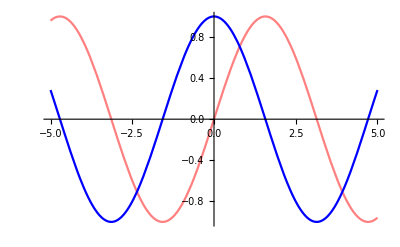

```mathematica
Plot[{Sin[x], Cos[x]},{x, -5, 5}, PlotStyle->{Pink, Blue}]
```

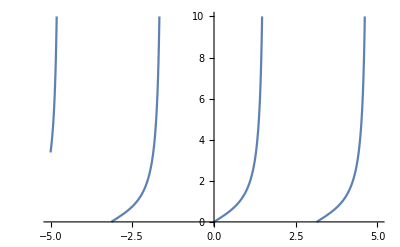

```mathematica
Plot[Tan[x],{x, -5, 5}, PlotRange->{0, 10}]
```

```mathematica
a = 0.1;
R[phi_] := Exp[a*phi];
```

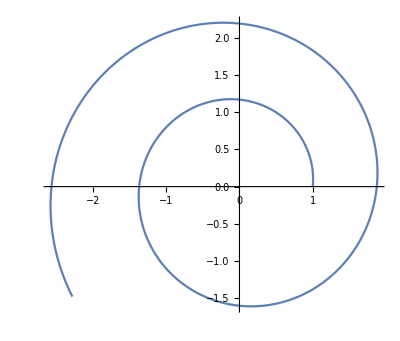

```mathematica
PolarPlot[R[phi], {phi, 0, 10}]
```

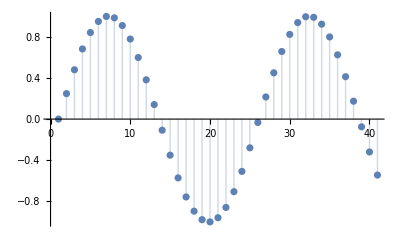

```mathematica
t = Table[Sin[x],{x,0,10, 1/4}];
ListPlot[t, Filling->Axis]
```

```mathematica
lm=LinearModelFit[t,Table[x^i, {i, 0, 4}],x]
```

FittedModel[-0.744672+0.6837 x-0.0845471 x^2+0.00334724 x^3-0.0000413892 x^4]

```mathematica
te = Map[Function[x,{x, 1/10}],t]
```

{{0,1/10},{Sin[1/4],1/10},{Sin[1/2],1/10},{Sin[3/4],1/10},{Sin[1],1/10},{Sin[5/4],1/10},{Sin[3/2],1/10},{Sin[7/4],1/10},{Sin[2],1/10},{Sin[9/4],1/10},{Sin[5/2],1/10},{Sin[11/4],1/10},{Sin[3],1/10},{Sin[13/4],1/10},{Sin[7/2],1/10},{Sin[15/4],1/10},{Sin[4],1/10},{Sin[17/4],1/10},{Sin[9/2],1/10},{Sin[19/4],1/10},{Sin[5],1/10},{Sin[21/4],1/10},{Sin[11/2],1/10},{Sin[23/4],1/10},{Sin[6],1/10},{Sin[25/4],1/10},{Sin[13/2],1/10},{Sin[27/4],1/10},{Sin[7],1/10},{Sin[29/4],1/10},{Sin[15/2],1/10},{Sin[31/4],1/10},{Sin[8],1/10},{Sin[33/4],1/10},{Sin[17/2],1/10},{Sin[35/4],1/10},{Sin[9],1/10},{Sin[37/4],1/10},{Sin[19/2],1/10},{Sin[39/4],1/10},{Sin[10],1/10}}

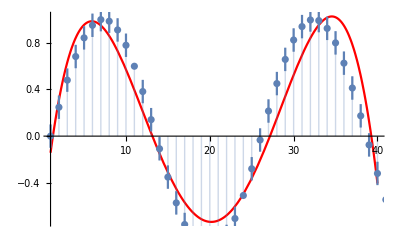

```mathematica
Needs["ErrorBarPlots`"];
Show[Plot[lm[x],{x,1,40}, PlotStyle->Red], ErrorListPlot[te,Filling->Axis]]
```

```mathematica
z = Sin[r]/r
```

Sin[r]/r

```mathematica
Sin[√(x^2+y^2)]/(√(x^2+y^2))
```

Sin[√(x^2+y^2)]/(√(x^2+y^2))

```mathematica
r=Sqrt[x^2+y^2]
```

√(x^2+y^2)

```mathematica
Plot3D[z,{x, -10, 10}, {y, -10, 10}, Mesh->30, PlotPoints->50, PlotRange->Full]
```

-Graphics3D-

```mathematica
a = 2;
b = 1;
A[v_] := a + b*Sin[v];
ParametricPlot3D[{A[v]*Cos[u],A[v]*Sin[u],b*Cos[v]}, {u, 0, 2*Pi}, {v, 0, 2*Pi}]
```

-Graphics3D-

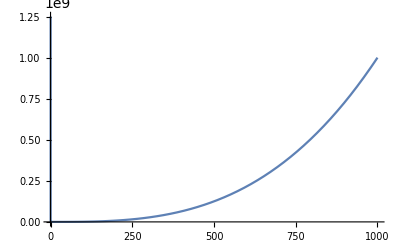

```mathematica
Plot[x^3 + x^(-5), {x, 10^(-3), 10^3}]
```

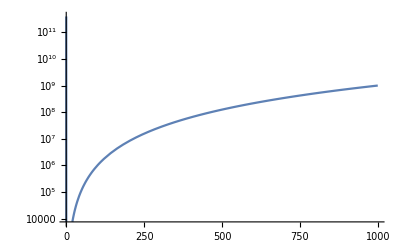

```mathematica
LogPlot[x^3 + x^(-5), {x, 10^(-3), 10^3}]
```

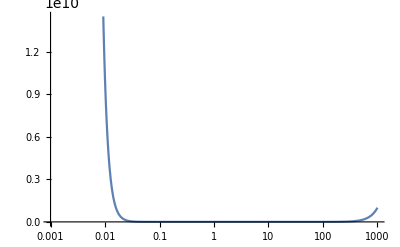

```mathematica
LogLinearPlot[x^3 + x^(-5), {x, 10^(-3), 10^3}]
```

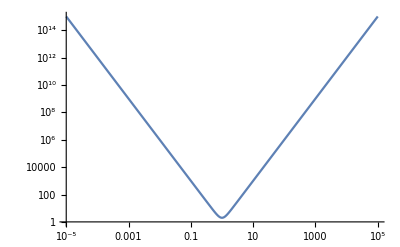

```mathematica
LogLogPlot[x^3+x^(-3),{x,10^(-5),10^5}]
```